```mathematica
R = 25;
ancho = 2;
```

```mathematica
ϕ[x_,y_]:= -Tanh[Sqrt[(x+.5)^2+(y+.5)^2]-R]/ancho;
```

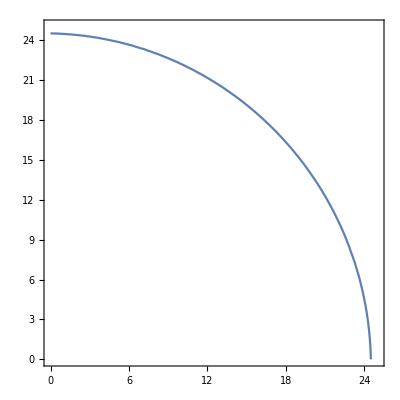

```mathematica
ContourPlot[ϕ[x,y]==0,{x,0,25},{y,0,25}]
```